```mathematica
Quit[];
```

```mathematica
DensityMat[k_,χ_,Na_,Nb_]:=Module[{SampleMat,H},
SampleMat=RandomVariate[CircularUnitaryMatrixDistribution[k×χ]];
H=Table[SampleMat[[(i-1)×χ+1;;i×χ,1;;χ]],{i,k}];
Table[Table[Module[{T1,T2},
T1=Fold[Dot,IdentityMatrix[χ],Map[H[[#+1]]&,Join[IntegerDigits[i,k,Na],IntegerDigits[l,k,Nb]]]];
T2=Fold[Dot,IdentityMatrix[χ],Map[H[[#+1]]&,Join[IntegerDigits[j,k,Na],IntegerDigits[l,k,Nb]]]];
Tr[T1]×Conjugate[Tr[T2]]
],{l,k^Nb}]//Total,{i,k^Na},{j,k^Na}]
];
VonNeumannEntropy[k_,χ_,Na_,Nb_]:=Map[-#×Log[#]&,Eigenvalues[DensityMat[k,χ,Na,Nb]]]//Total;
VonNeumannEntropyAvg[k_,χ_,Na_,Nb_]:=ParallelTable[VonNeumannEntropy[k,χ,Na,Nb],{1000}]//Mean;
VonNeumannEntropyAvgList[k_,χ_,Ns_]:=Table[{Na,Re[VonNeumannEntropyAvg[k,χ,Na,Ns-Na]]},{Na,0,Ns/2}];
```

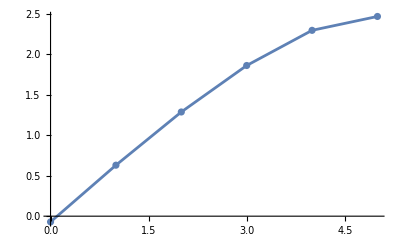

```mathematica
ListPlot[VonNeumannEntropyAvgList[2,6,10],Joined->True,Mesh->All]
```